```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
findEvolutionOperator[Ham_]:=(
n = Length[Ham];
funcs=Array[ψ[#2 + n*(#1- 1)][t]&,{n, n}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[n]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]]
)
shifts[B_, ω_] := NIntegrate[{(ω - Sqrt[4*B^2 + ω^2])/2, -(ω - Sqrt[4*B^2 + ω^2])/2}, {t, 0, Tmax}]
fidelity[M_] := (Tr[M.ConjugateTranspose[M]] + Abs[Tr[M]]^2)/(Length[M] + Length[M]^2)

hBar=1;
transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]
```

## One Frequency

H:

(0 | A+B ⅇ^(-ⅈ t ω)
A+B ⅇ^(ⅈ t ω) | Δ)

HF

(-ω | A | 0 | B | 0 | 0
A | Δ-ω | 0 | 0 | 0 | 0
0 | 0 | 0 | A | 0 | B
B | 0 | A | Δ | 0 | 0
0 | 0 | 0 | 0 | ω | A
0 | 0 | B | 0 | A | Δ+ω)

(0.867792-0.00714776 ⅈ | -0.133168+0.478699 ⅈ
-0.127564+0.480222 ⅈ | 0.744694+0.445584 ⅈ)

(0.376629-0.343395 ⅈ | -0.225738+0.830224 ⅈ
-0.225738+0.830224 ⅈ | 0.150891+0.486829 ⅈ)

(0.876186-0.00464256 ⅈ | -0.128446+0.472739 ⅈ
-0.128618+0.472692 ⅈ | 0.753201+0.447674 ⅈ)

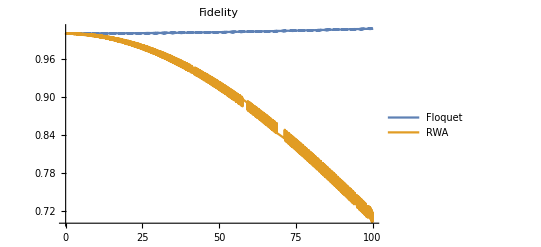

```mathematica
Clear[Δ, A, B, ω, H];

H0 = {{0, A},
{A, Δ}};

Hp1 = {{0, 0},
{B, 0}};

Hn1 = {{0, B},
{0, 0}};

H = H0 + Hp1*E^(ⅈ*ω*t) + Hn1*E^(-ⅈ*ω*t);

n = Length[H];
σI = IdentityMatrix[2];
HF = 0*IdentityMatrix[6];

getBlock[i_, j_, M_] := M[[{((Length[M]/n + 1)/2 + i)*n - (n - 1), ((Length[M]/n + 1)/2 + i)*n }, {((Length[M]/n + 1)/2 + j)*n - (n - 1), ((Length[M]/n + 1)/2 + j)*n }]]
setBlock[i_, j_, block_] := HF[[{((Length[HF]/n + 1)/2 + i)*n - (n - 1), ((Length[HF]/n + 1)/2 + i)*n }, {((Length[HF]/n + 1)/2 + j)*n - (n - 1), ((Length[HF]/n + 1)/2 + j)*n }]] = block

setBlock[-1, -1, H0 - ω*σI];
setBlock[0, 0, H0];
setBlock[1, 1, H0 + ω*σI];

setBlock[-1, 0, Hn1];
setBlock[0, 1, Hn1];
setBlock[0, -1, Hp1];
setBlock[1, 0, Hp1];

Print["H:"]
H // MatrixForm
Print["HF"]
HF // MatrixForm


Δ = 1;
A = 1;
B = 1;
ω = 60;


Tmax = 100;
Uexact = findEvolutionOperator[H];
URWA = findEvolutionOperator[H0];
UF = MatrixExp[-ⅈ*HF*t] // N;
UfromF = 0*IdentityMatrix[2];
Do[UfromF = UfromF + getBlock[i, 0, UF]*E^(ⅈ*i*ω*t)
,{i, -1, 1}];

Uexact /. t->Tmax // MatrixForm
URWA /. t->Tmax // MatrixForm
UfromF /. t->Tmax // MatrixForm

MF = ConjugateTranspose[Uexact].UfromF;
MRWA = ConjugateTranspose[Uexact].URWA;
Plot[{fidelity[MF], fidelity[MRWA]}, {t, 0, Tmax}, PlotLabel->"Fidelity", PlotLegends->{"Floquet", "RWA"}]
```

## Two Frequencies

H:

(0 | A+Ba ⅇ^(-ⅈ t ωa)+Bb ⅇ^(-ⅈ t ωb)
A+Ba ⅇ^(ⅈ t ωa)+Bb ⅇ^(ⅈ t ωb) | Δ)

HF:

(-ωa | A | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0
A | Δ-ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ωb | A | 0 | Bb | 0 | 0 | 0 | 0
0 | 0 | A | Δ-ωb | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | A | 0 | Bb | 0 | Ba
Ba | 0 | Bb | 0 | A | Δ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ωb | A | 0 | 0
0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωb | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa | A
0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | A | Δ+ωa)

exact

(0.934543+0.332744 ⅈ | 0.0285464-0.122868 ⅈ
0.0375999-0.120406 ⅈ | 0.974364+0.186289 ⅈ)

Floquet - fidelity 1.03788 + 0. I

(0.951189+0.344956 ⅈ | 0.0347386-0.114208 ⅈ
0.0278751-0.116074 ⅈ | 0.994902+0.184188 ⅈ)

RWA - fidelity 0.344472 + 0. I

(0.376629-0.343395 ⅈ | -0.225738+0.830224 ⅈ
-0.225738+0.830224 ⅈ | 0.150891+0.486829 ⅈ)

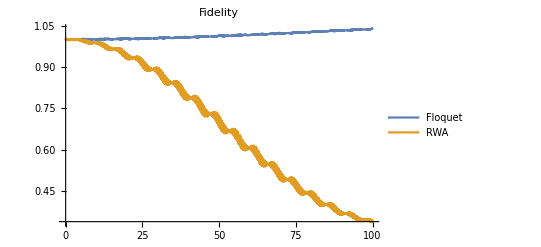

```mathematica
Clear[Δ, A, Ba, Bb, ωa, ωb, H];

H0 = {{0, A},
{A, Δ}};

Hp1a = {{0, 0},
{Ba, 0}};

Hn1a = {{0, Ba},
{0, 0}};

Hp1b = {{0, 0},
{Bb, 0}};

Hn1b = {{0, Bb},
{0, 0}};

H = H0 + Hp1a*E^(ⅈ*ωa*t) + Hn1a*E^(-ⅈ*ωa*t) + Hp1b*E^(ⅈ*ωb*t) + Hn1b*E^(-ⅈ*ωb*t);

n = Length[H];
σI = IdentityMatrix[2];
HF = 0*IdentityMatrix[10];

getBlock[i_, j_, M_] := M[[{((Length[M]/n + 1)/2 + i)*n - (n - 1), ((Length[M]/n + 1)/2 + i)*n }, {((Length[M]/n + 1)/2 + j)*n - (n - 1), ((Length[M]/n + 1)/2 + j)*n }]]
setBlock[i_, j_, block_] := HF[[{((Length[HF]/n + 1)/2 + i)*n - (n - 1), ((Length[HF]/n + 1)/2 + i)*n }, {((Length[HF]/n + 1)/2 + j)*n - (n - 1), ((Length[HF]/n + 1)/2 + j)*n }]] = block

setBlock[-2, -2, H0 - ωa*σI];
setBlock[-1, -1, H0 - ωb*σI];
setBlock[0, 0, H0];
setBlock[1, 1, H0 + ωb*σI];
setBlock[2, 2, H0 + ωa*σI];

setBlock[-2, 0, Hn1a];
setBlock[0, 2, Hn1a];
setBlock[0, -2, Hp1a];
setBlock[2, 0, Hp1a];

setBlock[-1, 0, Hn1b];
setBlock[0, 1, Hn1b];
setBlock[0, -1, Hp1b];
setBlock[1, 0, Hp1b];

Print["H:"]
H // MatrixForm
Print["HF:"]
HF // MatrixForm

Δ = 1;
A = 1;
Ba = 1;
Bb = 1;
ωa = 60;
ωb = 61;


Tmax = 100;
Uexact = findEvolutionOperator[H];
URWA = findEvolutionOperator[H0];
UF = MatrixExp[-ⅈ*HF*t] // N;

UfromF = 0*IdentityMatrix[2];
ωs = {-ωa, -ωb, 0, ωb, ωa};
Do[UfromF = UfromF + getBlock[i, 0, UF]*E^(ⅈ*ωs[[i + 3]]*t)
,{i, -2, 2}];

MF = ConjugateTranspose[Uexact].UfromF;
MRWA = ConjugateTranspose[Uexact].URWA;

Print["exact"]
Uexact /. t->Tmax // MatrixForm
Print["Floquet - fidelity " <> ToString[fidelity[MF /. t->Tmax]]]
UfromF /. t->Tmax  // MatrixForm
Print["RWA - fidelity " <> ToString[fidelity[MRWA /. t->Tmax]]]
URWA /. t->Tmax  // MatrixForm

Plot[{fidelity[MF], fidelity[MRWA]}, {t, 0, Tmax}, PlotLabel->"Fidelity", PlotLegends->{"Floquet", "RWA"}]
```

## Two frequencies, but with another order of term

H:

(0 | A+Ba ⅇ^(-ⅈ t ωa)+Bb ⅇ^(-ⅈ t ωb)
A+Ba ⅇ^(ⅈ t ωa)+Bb ⅇ^(ⅈ t ωb) | Δ)

HF:

(-2 ωa | A | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
A | Δ-2 ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ωa-ωb | A | 0 | 0 | 0 | Bb | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | A | Δ-ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 ωb | A | 0 | 0 | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | A | Δ-2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ωa | A | 0 | 0 | 0 | Bb | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ba | 0 | Bb | 0 | 0 | 0 | A | Δ-ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωb | A | 0 | 0 | 0 | Bb | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ba | 0 | Bb | 0 | 0 | 0 | A | Δ-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa+ωb | A | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | 0 | 0 | A | Δ-ωa+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | 0 | 0 | 0 | Bb | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | Bb | 0 | 0 | 0 | A | Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa-ωb | A | 0 | 0 | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | A | Δ+ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωb | A | 0 | 0 | 0 | Bb | 0 | Ba | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | Bb | 0 | 0 | 0 | A | Δ+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa | A | 0 | 0 | 0 | Bb | 0 | Ba
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | Bb | 0 | 0 | 0 | A | Δ+ωa | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωb | A | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | 0 | 0 | A | Δ+2 ωb | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa+ωb | A | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | Bb | 0 | 0 | 0 | A | Δ+ωa+ωb | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωa | A
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | A | Δ+2 ωa)

exact

(0.934543+0.332744 ⅈ | 0.0285464-0.122868 ⅈ
0.0375999-0.120406 ⅈ | 0.974364+0.186289 ⅈ)

Floquet - fidelity 0.999989 + 0. I

(0.936928+0.32424 ⅈ | 0.0279284-0.128018 ⅈ
0.0407431-0.124535 ⅈ | 0.972027+0.194886 ⅈ)

RWA - fidelity 0.344472 + 0. I

(0.376629-0.343395 ⅈ | -0.225738+0.830224 ⅈ
-0.225738+0.830224 ⅈ | 0.150891+0.486829 ⅈ)

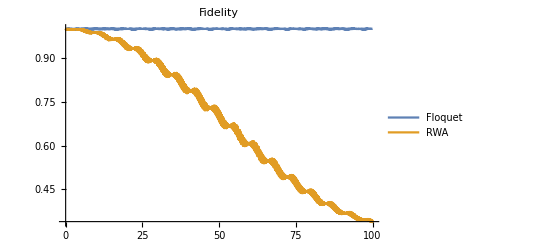

```mathematica
Clear[Δ, A, Ba, Bb, ωa, ωb, H];

H0 = {{0, A},
{A, Δ}};

Hp1a = {{0, 0},
{Ba, 0}};

Hn1a = {{0, Ba},
{0, 0}};

Hp1b = {{0, 0},
{Bb, 0}};

Hn1b = {{0, Bb},
{0, 0}};

H = H0 + Hp1a*E^(ⅈ*ωa*t) + Hn1a*E^(-ⅈ*ωa*t) + Hp1b*E^(ⅈ*ωb*t) + Hn1b*E^(-ⅈ*ωb*t);

n = Length[H];
σI = IdentityMatrix[2];
blockOrder = {-2ωa, -ωa - ωb, -2ωb, -ωa,-ωb, -ωa + ωb, 0, ωa - ωb, ωb, ωa, 2ωb, ωa + ωb, 2ωa};
l =  (Length[blockOrder] + 1)/2;
HF = 0*IdentityMatrix[2*Length[blockOrder]];

getBlock[i_, j_, M_] := M[[{((Length[M]/n + 1)/2 + i)*n - (n - 1), ((Length[M]/n + 1)/2 + i)*n }, {((Length[M]/n + 1)/2 + j)*n - (n - 1), ((Length[M]/n + 1)/2 + j)*n }]]
setBlock[i_, j_, block_] := HF[[{((Length[HF]/n + 1)/2 + i)*n - (n - 1), ((Length[HF]/n + 1)/2 + i)*n }, {((Length[HF]/n + 1)/2 + j)*n - (n - 1), ((Length[HF]/n + 1)/2 + j)*n }]] = block

Do[
setBlock[i, i, H0 + blockOrder[[i + l]]*σI]
,{i, -(l - 1), l - 1}];

Clear[i, j]
Do[
Do[(
If[blockOrder[[i + l]] - blockOrder[[j + l]] == -ωa, setBlock[i, j, Hn1a]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == ωa, setBlock[i, j, Hp1a]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == -ωb, setBlock[i, j, Hn1b]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == ωb, setBlock[i, j, Hp1b]];
),{j, -(l -1), l - 1}]
,{i, -(l - 1), l - 1}]

Print["H:"]
H // MatrixForm
Print["HF:"]
HF // MatrixForm

Δ = 1;
A = 1;
Ba = 1;
Bb = 1;
ωa = 60;
ωb = 61;


Tmax = 100;
Uexact = findEvolutionOperator[H];
URWA = findEvolutionOperator[H0];
UF = MatrixExp[-ⅈ*HF*t] // N;

UfromF = 0*IdentityMatrix[2];
Do[UfromF = UfromF + getBlock[i, 0, UF]*E^(ⅈ*blockOrder[[i + l]]*t)
,{i, -(l - 1), (l - 1)}];

MF = ConjugateTranspose[Uexact].UfromF;
MRWA = ConjugateTranspose[Uexact].URWA;

Print["exact"]
Uexact /. t->Tmax // MatrixForm
Print["Floquet - fidelity " <> ToString[fidelity[MF /. t->Tmax]]]
UfromF /. t->Tmax  // MatrixForm
Print["RWA - fidelity " <> ToString[fidelity[MRWA /. t->Tmax]]]
URWA /. t->Tmax  // MatrixForm

Plot[{fidelity[MF], fidelity[MRWA]}, {t, 0, Tmax}, PlotLabel->"Fidelity", PlotLegends->{"Floquet", "RWA"}]
```

## Two frequencies, but with third-order terms - very slow

```mathematica
Clear[Δ, A, Ba, Bb, ωa, ωb, H];

H0 = {{0, A},
{A, Δ}};

Hp1a = {{0, 0},
{Ba, 0}};

Hn1a = {{0, Ba},
{0, 0}};

Hp1b = {{0, 0},
{Bb, 0}};

Hn1b = {{0, Bb},
{0, 0}};

H = H0 + Hp1a*E^(ⅈ*ωa*t) + Hn1a*E^(-ⅈ*ωa*t) + Hp1b*E^(ⅈ*ωb*t) + Hn1b*E^(-ⅈ*ωb*t);

n = Length[H];
σI = IdentityMatrix[2];

termOrder = 3;
blockOrder = Table[Table[k*ωb, {k, -(termOrder - Abs[kk]), (termOrder - Abs[kk])}] + kk*ωa, {kk, -termOrder, termOrder}] // Flatten;
ord = blockOrder /. {ωa -> 100, ωb -> 99} // Ordering;
blockOrder[[ord]]

l =  (Length[blockOrder] + 1)/2;
HF = 0*IdentityMatrix[2*Length[blockOrder]];

getBlock[i_, j_, M_] := M[[{((Length[M]/n + 1)/2 + i)*n - (n - 1), ((Length[M]/n + 1)/2 + i)*n }, {((Length[M]/n + 1)/2 + j)*n - (n - 1), ((Length[M]/n + 1)/2 + j)*n }]]
setBlock[i_, j_, block_] := HF[[{((Length[HF]/n + 1)/2 + i)*n - (n - 1), ((Length[HF]/n + 1)/2 + i)*n }, {((Length[HF]/n + 1)/2 + j)*n - (n - 1), ((Length[HF]/n + 1)/2 + j)*n }]] = block

Do[
setBlock[i, i, H0 + blockOrder[[i + l]]*σI]
,{i, -(l - 1), l - 1}];

Clear[i, j]
Do[
Do[(
If[blockOrder[[i + l]] - blockOrder[[j + l]] == -ωa, setBlock[i, j, Hn1a]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == ωa, setBlock[i, j, Hp1a]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == -ωb, setBlock[i, j, Hn1b]];
If[blockOrder[[i + l]] - blockOrder[[j + l]] == ωb, setBlock[i, j, Hp1b]];
),{j, -(l -1), l - 1}]
,{i, -(l - 1), l - 1}]

Print["H:"]
H // MatrixForm
Print["HF:"]
HF // MatrixForm

Δ = 1;
A = 1;
Ba = 1;
Bb = 1;
ωa = 60;
ωb = 61;


Tmax = 100;
Uexact = findEvolutionOperator[H];
URWA = findEvolutionOperator[H0];
UF = findEvolutionOperator[HF];

UfromF = 0*IdentityMatrix[2];
Do[UfromF = UfromF + getBlock[i, 0, UF]*E^(ⅈ*blockOrder[[i + l]]*t)
,{i, -(l - 1), (l - 1)}];

MF = ConjugateTranspose[Uexact].UfromF;
MRWA = ConjugateTranspose[Uexact].URWA;

Print["exact"]
Uexact /. t->Tmax // MatrixForm
Print["Floquet - fidelity " <> ToString[fidelity[MF /. t->Tmax]]]
UfromF /. t->Tmax  // MatrixForm
Print["RWA - fidelity " <> ToString[fidelity[MRWA /. t->Tmax]]]
URWA /. t->Tmax  // MatrixForm

Plot[{fidelity[MF], fidelity[MRWA]}, {t, 0, Tmax}, PlotLabel->"Fidelity", PlotLegends->{"Floquet", "RWA"}]
```

{-3 ωa,-2 ωa-ωb,-ωa-2 ωb,-3 ωb,-2 ωa,-ωa-ωb,-2 ωb,-2 ωa+ωb,-ωa,-ωb,ωa-2 ωb,-ωa+ωb,0,ωa-ωb,-ωa+2 ωb,ωb,ωa,2 ωa-ωb,2 ωb,ωa+ωb,2 ωa,3 ωb,ωa+2 ωb,2 ωa+ωb,3 ωa}

H:

(0 | A+Ba ⅇ^(-ⅈ t ωa)+Bb ⅇ^(-ⅈ t ωb)
A+Ba ⅇ^(ⅈ t ωa)+Bb ⅇ^(ⅈ t ωb) | Δ)

HF:

(-3 ωa | A | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
A | Δ-3 ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ωa-ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | A | Δ-2 ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 ωa | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ba | 0 | Bb | 0 | A | Δ-2 ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ωa+ωb | A | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Bb | 0 | A | Δ-2 ωa+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa-2 ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | Δ-ωa-2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa-ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa+ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-ωa+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωa+2 ωb | A | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-ωa+2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | Δ-3 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωb | A | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+3 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa-2 ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | Δ+ωa-2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa-ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωa | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa+ωb | A | 0 | Bb | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωa+ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωa+2 ωb | A | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+ωa+2 ωb | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωa-ωb | A | 0 | Bb | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | A | Δ+2 ωa-ωb | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωa | A | 0 | Bb | 0 | Ba
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+2 ωa | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωa+ωb | A | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | 0 | 0 | Bb | 0 | A | Δ+2 ωa+ωb | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ωa | A
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ba | 0 | 0 | 0 | A | Δ+3 ωa)